## Connexion DLL

## DLL

```mathematica
Clear[pathToDll]
```

```mathematica
Needs["NETLink`"];
```

```mathematica
InstallNET[];
```

```mathematica
pathToDll="C:\\Users\\Clem\\Documents\\ESGI\\projet_annuel_ibd3a\\C++_lib\\Dll-Machine-Learning\\x64\\Debug\\Dll-Machine-Learning.dll";
```

```mathematica
return42ExternFunc=DefineDLLFunction["return42",pathToDll,"int",{}];
```

```mathematica
return42ExternFunc[]
```

42

## Définitions Méthodes C++

```mathematica
Clear[createLinearModel, linearFitClassificationRosenblatt, linearClassify, linearCreateAndFitRegression, linearPredict, createMlp, classify, fitClassification, predict, eraseMlp, getOutputsforRegression];
```

### Perceptron Linéaire

#### Création modèle

```mathematica
createLinearModel = DefineDLLFunction["createLinearModel", pathToDll, "System.IntPtr", {"int", "int"}];
```

#### Classification Linéaire Rosenblatt

```mathematica
linearFitClassificationRosenblatt = DefineDLLFunction["linearFitClassificationRosenblatt", pathToDll, "int", {"System.IntPtr", "double[]", "int", "int", "double[]", "int", "int", "double"}];
```

```mathematica
linearClassify =  DefineDLLFunction["linearClassify", pathToDll, "double", {"System.IntPtr", "double[]", "int", "double[]", "int"}];
```

#### Régression linéaire

```mathematica
linearCreateAndFitRegression = DefineDLLFunction["linearCreateAndFitRegression", pathToDll, "void", {"System.IntPtr", "double[]", "int", "int", "double[]","int"}];
```

```mathematica
linearPredict = DefineDLLFunction["linearPredict", pathToDll, "void", {"System.IntPtr", "double[]", "int", "double[]", "int"}];
```

#### Perceptron Multi - Couches

```mathematica
createMlp=DefineDLLFunction["createMlp",pathToDll,"System.IntPtr",{"int[]","int"}];
```

```mathematica
classify=DefineDLLFunction["classify",pathToDll,"void",{"System.IntPtr","double[]","int"}];
```

```mathematica
fitClassification=DefineDLLFunction["fitClassification",pathToDll,"void",{"System.IntPtr","double[]","int","int","double[]","int"}];
```

```mathematica
predict=DefineDLLFunction["predict",pathToDll,"void",{"System.IntPtr","double[]","int"}];
```

```mathematica
eraseMlp=DefineDLLFunction["eraseMlp",pathToDll,"void",{"System.IntPtr"}];
```

```mathematica
getOutputsforRegression=DefineDLLFunction["getOutputsforRegression",pathToDll,"double",{"System.IntPtr"}];
```

## Cas de tests

### Simple Linéaire Séparable

```mathematica
Clear[a,b,c,positivePointsL, negativePointsL, f];
```

```mathematica
a = RandomInteger[{-5; 5}];
b= RandomInteger[{-5; 5}];
c= RandomInteger[{-5; 5}];
```

```mathematica
f[x_] := -a/b*x+c/b
```

```mathematica
positivePointsL = Table[x= RandomReal[{-5, 5}]; {x, f[x] + RandomReal[{0.5, 2}]}, {i,1, 3}]
```

{{1.63885,0.88562},{0.192232,2.88606},{-4.98215,11.4027}}

```mathematica
negativePointsL = Table[x = RandomReal[{-5, 5}];
{x, f[x]-RandomReal[{0.5, 2 }]}, {i,1,3}]
```

{{4.68564,-5.216},{0.260122,0.276761},{0.221979,0.773068}}

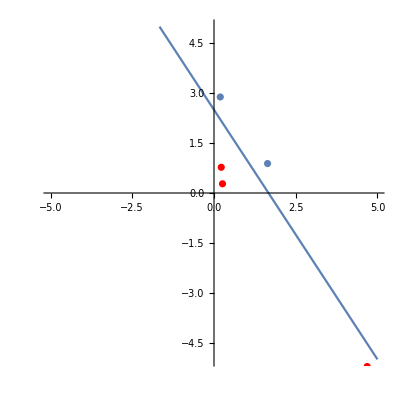

```mathematica
Show[Plot[f[x], {x,-5, 5}, PlotRange->{-5,5},
AspectRatio->1],
ListPlot[negativePointsL, PlotStyle->Red],
ListPlot[positivePointsL]]
```

### Simple non linéairement séparable

```mathematica
Clear[redPointsL, bluePointsL];
```

```mathematica
redPointsL = {positivePointsL[[1]], positivePointsL[[2]], negativePointsL[[1]]}
bluePointsL = {positivePointsL[[3]], negativePointsL[[2]], negativePointsL[[3]]}
```

{{1.63885,0.88562},{0.192232,2.88606},{4.68564,-5.216}}

{{-4.98215,11.4027},{0.260122,0.276761},{0.221979,0.773068}}

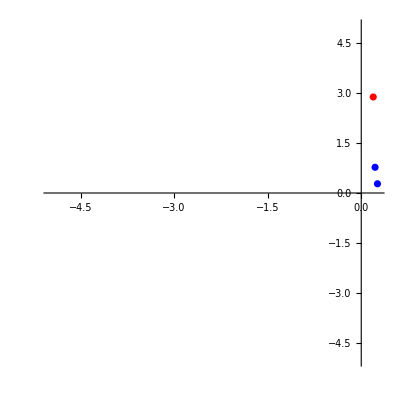

```mathematica
Show[ListPlot[bluePointsL, PlotStyle->Blue,AspectRatio->1, PlotRange->{-5, 5}], ListPlot[redPointsL, PlotStyle->Red]]
```

### Cross

```mathematica
Clear[left,right,top, down];
```

```mathematica
left[x_] = (-1)*Abs[a*x];
right[x_] = Abs[a*x];
top [x_]= Abs[a];
down [x_]= (-1) * Abs[a];
```

```mathematica
rand = RandomReal[{-5,5}];
```

```mathematica
rightHighPoints = Table[x = rand;
{right[x]+RandomReal[{0.5,2}], top[x]+RandomReal[{0.5,2}]},{i,1,15}];
rightDownPoints = Table[x = rand;
{right[x]+RandomReal[{0.5,2}], down[x]-RandomReal[{0.5,2}]},{i,1,15}];
leftHighPoints = Table[x = rand;
{left[x]-RandomReal[{0.5,2}], top[x]+RandomReal[{0.5,2}]},{i,1,15}];
leftDownPoints = Table[x = RandomReal[{-5,5}];
{left[x]-RandomReal[{0.5,2}], down[x]-RandomReal[{0.5,2}]},{i,1,15}];
```

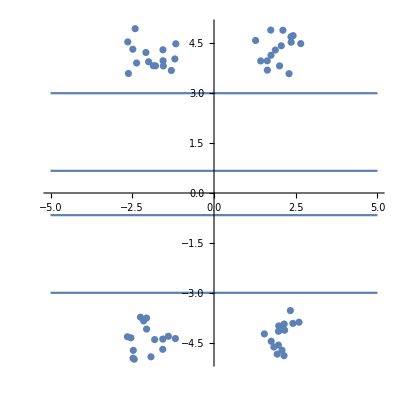

```mathematica
Show[Plot[left[x], {x, -5, 5}, PlotRange->{-5,5}, AspectRatio->1],
Plot[top[x], {x, -5, 5}], Plot[right[x], {x, -5, 5}], Plot[down[x], {x, -5, 5}],
ListPlot[rightDownPoints], ListPlot[rightHighPoints], ListPlot[leftDownPoints], ListPlot[leftHighPoints]]
```

### XOR

```mathematica
Clear[a, Pmc, Xxor, Yxor,test]
```

```mathematica
a = RandomInteger[{-5, 5}]
red = {{a, -a}, {-a, a}}
blue = {{-a, -a},{a,a}}
```

2

{{2,-2},{-2,2}}

{{-2,-2},{2,2}}

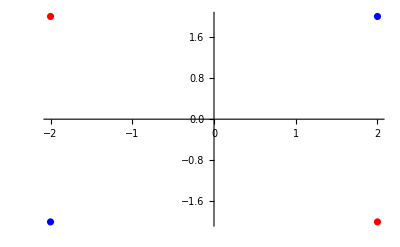

```mathematica
Show[ListPlot[red, PlotStyle-> Red],ListPlot[blue, PlotStyle->Blue]]
```

```mathematica
Xxor = {{-1,1},{1,-1},{1,1},{-1,-1}};
Yxor = {-1, -1, 1, 1}
```

{-1,-1,1,1}

### Utilisation méthodes

```mathematica
Clear[model, X, Y, Xtest, Xtest2, Y, Ytest]
```

```mathematica
model = createLinearModel[2,1];
```

```mathematica
X=Flatten[{positivePointsL, negativePointsL}]
Y = {1,1,1, -1,-1,-1}
```

{1.63885,0.88562,0.192232,2.88606,-4.98215,11.4027,4.68564,-5.216,0.260122,0.276761,0.221979,0.773068}

{1,1,1,-1,-1,-1}

```mathematica
Xtest = {X[[1]], X[[2]]}
Ytest = {Y[[1]]}
```

{1.63885,0.88562}

{1}

```mathematica
linearFitClassificationRosenblatt[model, X, 12, 2, Y, 1, 1000, 0.1];
```

```mathematica
linearClassify[model, Xtest, 2, Ytest, 1];
```

```mathematica
Xtest2 = Partition[Flatten[Table[{i,j},{i, -5, 5, 0.2}, {j, -5, 5, 0.2}]], 2]
```

{{-5.,-5.},{-5.,-4.8},{-5.,-4.6},{-5.,-4.4},{-5.,-4.2},{-5.,-4.},{-5.,-3.8},{-5.,-3.6},{-5.,-3.4},{-5.,-3.2},{-5.,-3.},{-5.,-2.8},{-5.,-2.6},2576,{5.,2.8},{5.,3.},{5.,3.2},{5.,3.4},{5.,3.6},{5.,3.8},{5.,4.},{5.,4.2},{5.,4.4},{5.,4.6},{5.,4.8},{5.,5.}}
 |  |  |  |

```mathematica
positive = Select[Xtest2,linearClassify[model, #,2, Ytest,1 ]== 1&];
negative =Select[Xtest2,linearClassify[model, #,2, Ytest,1 ]== -1&];
```

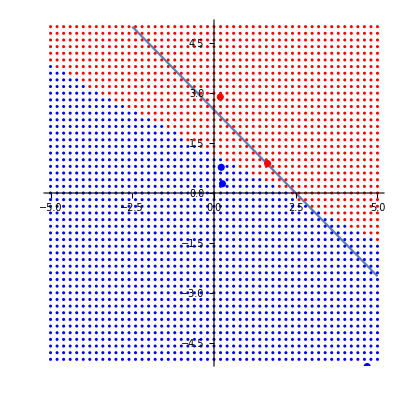

```mathematica
Show[Plot[f[x], {x,-5, 5}, PlotRange->{-5,5},
AspectRatio->1],ListPlot[positive, PlotStyle->Red], ListPlot[negative, PlotStyle->Blue], ListPlot[negativePointsL, PlotStyle->Blue, PlotStyle->Thick],
ListPlot[positivePointsL, PlotStyle->Red, PlotStyle->Thick]]
```

```mathematica
managedTab = NETNew["int[]", 5]
LoadNETType["System.Runtime.InteropServices.Marshal"]
Marshal`Copy[funct, managedTab, 0, 5]
managedTab@GetValue[2]
```

```mathematica
copyFromNetArray[array_] := Table[array@GetValue[i], {i, 0, array@Length-1}]
```

```mathematica
NETObjectToExpression[managedTab]
```